## Wolfram Language Extentions

```mathematica
fN[x_]:=If[x==Round[x],IntegerPart[x],N[x]];(*format number*)
fN[x_,precision_]:=If[Abs[x-Round[x]]<=precision,Round[x],N[x]];
```

## General Functions

```mathematica
diceP[p_,n_,s_]:=1/s^n∑_(k=0)^⌊(p-n)/s⌋ (-1)^k Binomial[n,k]Binomial[p-s k -1,p-s k-n];
diceSumP[minSum_,n_,s_]:=∑_(i=minSum)^(n s) diceP[i,n,s];
diceSums=Table[{s,diceSumP[s,2,6]},{s,1,13}];
pSuccess[dc_]:=Max[Min[1/20+(20-dc)/20,19/20],1/20];
pSuccess[dc_,"lucky"]:=pSuccess[dc,"advantage"];
pSuccess[dc_,adv_]:=If[adv=="advantage",pSuccess[dc]+(1-pSuccess[dc])pSuccess[dc],If[adv=="disadvantage",pSuccess[dc]^2,pSuccess[dc]]];
pSuccess[dc_,"superdisadvantage"]:=pSuccess[dc,"disadvantage"] pSuccess[dc];
pSuccess[dc_,adv_,"lucky"]:=pSuccess[dc,adv]+(1-pSuccess[dc,adv])pSuccess[dc];
pSuccess[dc_,"superadvantage"]:=pSuccess[dc,"advantage","lucky"];
d[n_]:=(1+n)/2;
pSuccessNoNats[dc_]:=Max[Min[1/20+(20-dc)/20,1],0];
pSuccessNoNats[dc_,"lucky"]:=pSuccessNoNats[dc,"advantage"];
pSuccessNoNats[dc_,adv_]:=If[adv=="advantage",pSuccessNoNats[dc]+(1-pSuccessNoNats[dc])pSuccessNoNats[dc],If[adv=="disadvantage",pSuccessNoNats[dc]^2,pSuccessNoNats[dc]]];
pSuccessNoNats[dc_,"superdisadvantage"]:=pSuccessNoNats[dc,"disadvantage"] pSuccessNoNats[dc];
pSuccessNoNats[dc_,adv_,"lucky"]:=pSuccessNoNats[dc,adv]+(1-pSuccessNoNats[dc,adv])pSuccessNoNats[dc];
pSuccessNoNats[dc_,"superadvantage"]:=pSuccessNoNats[dc,"advantage","lucky"];
pSuccessBuffed[dc_,modifier_,0]:=pSuccess[dc,modifier];
pSuccessBuffed[dc_,modifier_,d_]:=∑_(i=1)^d (pSuccess[dc-i,modifier]/d);
pSuccessBuffedNoNats[dc_,modifier_,d_]:=∑_(i=1)^d (pSuccessNoNats[dc-i,modifier]/d);
pSuccessBuffedBuffed[dc_,modifier_,d1_,d2_]:=∑_(i=1)^d2 (pSuccessBuffed[dc-i,modifier,d1]/d2);
pSuccessBuffedBuffedNoNats[dc_,modifier_,d1_,d2_]:=∑_(i=1)^d2 (pSuccessBuffedNoNats[dc-i,modifier,d1]/d2);
hDOS[damage_,saveDC_,conditions_]:=(1-pSuccessNoNats[saveDC-conditions[save]])damage+pSuccessNoNats[saveDC-conditions[save]] damage/2;
hDOS[damage_,saveDC_]:=hDOS[damage,saveDC,defaultConditions[[1,2]]];
distance[a_,b_,c_]:=N[√(a^2+b^2+c^2)];
distance[a_,b_]:=distance[a,b,0];
dZQ[xy_,m_]:=N[√(m^2-xy^2)];(*how much change in height can one move with movement of m moving xy horizontally?*)
radiusConeProjectionCircle[range_]:= range Cos[Pi-ArcTan[1/2]-Pi/2];
roll[n_,dN_]:=Table[RandomInteger[{1,dN}],n];
pKSuccessesInNTrials[k_,n_,p_]:=Binomial[n,k] p^k(1-p)^(n-k);
pAtLeastKSuccessesInNTrials[k_,n_,p_]:=1-∑_(i=0)^(k-1) pKSuccessesInNTrials[i,n,p];
avgHighest[1,s_]:=d[s];
avgHighest[2,s_]:=1/(6 s)(s+1)(4s-1);
avgHighest[3,s_]:=1/(4s)(s+1)(3s-1);
avgHighest[4,s_]:=1/(30 s^3)(s+1)(24 s^3-9 s^2-s+1);
avgLowest[n_,s_]:=(s+1)-avgHighest[n,s];
contestedCheck[challenger_,challenged_]:=Total[Flatten[Table[If[a+challenger>b+challenged,1,0],{a,1,20},{b,1,20}]]]/400;
pNo20[n_,level_]:=(19/20)^(If[level<14,2,3]n);(*probability of not getting a 20 with Portent in n days*)
pNo20[n_]:=pNo20[n,1];
pAtLeastOneK[k_,n_]:=1-(1-((20-(k-1))/20))^n;(*probability of getting at least one k in n tries*)
proficiencyBonus[level_]:=Ceiling[level/4]+1;
(*advantageModifiers={{"superAdvantage",3},{"advantage",2},{"normal",1},{"disadvantage",1/2},{"superDisadvantage",1/3}};*)
rSphereCut[r_,h_]:=√(r^2-(r-(r-h))^2);
timeTravel[feet_]:=Quantity[feet/300,"Minutes"];
timeTravelMiles[miles_,speed_]:=Quantity[miles/Switch[speed,"slow",2,"normal",3,"fast",4],MixedUnit[{"Hours","Minutes"}]];
timeSpecialTravelPaceTravel[miles0_,movement0_,speed0_]:=(*speed [slow,normal,fast]*)
Module[{miles=miles0,movement=movement0,speed=If[speed0=="slow",2,If[speed0=="fast",4,3]]},
UnitConvert[Quantity[miles/(movement/30 speed),"Hours"],MixedUnit[{"Hours","Minutes"}]]
];
abilityModifier[score_]:=Floor[(score-10)/2];
```

### Unit Tests

```mathematica
runTests[doRun_]:=With[{runTests=doRun},
If[runTests,testReport=TestReport[{
VerificationTest[pSuccess[1],19/20,TestID->1],
VerificationTest[pSuccess[20],1/20,TestID->2],
VerificationTest[pSuccess[21],1/20,TestID->3],
VerificationTest[pSuccessNoNats[1],1,TestID->4],
VerificationTest[pSuccessNoNats[21],0,TestID->5],
VerificationTest[pSuccess[20,"advantage"],1-(19/20)^2,TestID->6],
VerificationTest[pSuccess[20,"superadvantage"],1-(19/20)^3,TestID->7],
VerificationTest[pSuccess[30,"disadvantage"],1/20^2,TestID->8],
VerificationTest[pSuccess[30,"superdisadvantage"],1/20^3,TestID->9],
VerificationTest[hDOS[1,23,defaultConditions[[1,2]]],1,TestID->10],
VerificationTest[hDOS[1,22,defaultConditions[[1,2]]],19/20+1/(20 2),TestID->11],
VerificationTest[hDOS[1,3,defaultConditions[[1,2]]],1/2,TestID->12],
VerificationTest[pSuccessBuffedNoNats[24,"normal",4],1/80,TestID->13],
VerificationTest[pSuccessBuffedNoNats[25,"normal",4],0,TestID->14],
VerificationTest[pSuccessBuffed[25,"normal",4],1/20,TestID->15]
}],Nothing]
];
```

```mathematica
runTests[True]["AllTestsSucceeded"]
```

False

## Rule Functions

```mathematica
auraOfVitality[lifeCleric_]:=2d[6]+If[lifeCleric,5,0];
auraOfVitalitySum[lifeCleric_,metamagic_]:=10 auraOfVitality[lifeCleric] If[metamagic,2,1];
avgGreatWeaponFighting[d_]:=Mean[(If[#[[1]]<3,#[[2]],#[[1]]])& /@ Flatten[Table[{a,b},{a,1,d},{b,1,d}],1]];
spiritShroudDamage[level_]:=If[level<3,0,(Floor[(level-3)/2]+1)d[8]];
damageEldritchBlast[level_,charBonus_,hex_,spiritShroud_]:=(Floor[(level+1)/6]+1)(d[10]+If[level>1,charBonus,0]+hex d[6]+spiritShroud spiritShroudDamage[If[level<5,0,If[level<9,3,5]]]);(*charBonus=0 for not having AgonizingBlast*)
eldritchBlastBeams[level_]:=If[level<5,1,If[level<11,2,If[level<17,3,4]]];
cureWounds[level_,scaMod_,lifeCleric_,beaconOfHope_]:=level If[beaconOfHope==1,8,d[8]]+scaMod+(lifeCleric (level+2));
cureWounds[level_,scaMod_]:=cureWounds[level,scaMod,0,0];
healingWord[level_,scaMod_,lifeCleric_,beaconOfHope_]:=level If[beaconOfHope==1,4,d[4]]+scaMod+(lifeCleric (level+2));
preserveLife[classLevel_]:=If[classLevel>=2,5 classLevel,0];
heal[lifeCleric_]:=70+(lifeCleric (6+2));
regenerate[lifeCleric_,turns_,beaconOfHope_]:=If[beaconOfHope==1,4 8+15,4d[8]+15]+(lifeCleric (7+2))+turns (1+lifeCleric (7+2));
rageDamage[level_]:=If[level<=8,2,If[level<=15,3,4]];
barbarianDmg[level_,berserker_,gwm_]:=(*enter level gwm becomes available, 0 if never*)If[level<2&&gwm==1,With[{ac=14},fN[pSuccess[ac-5+5]/pSuccess[ac-5]]],1]((If[level<5,1,2]+If[level>=3,berserker,0])(d[12]+If[level<4,3,If[level<9,4,5]]+rageDamage[level]+If[gwm==0,0,If[level>=gwm,10,0]]));
sneakAttack[level_]:=Ceiling[level/2]d[6];
magicMissileDamage[level_,intBonus_,empowered_]:=(level+2)(d[4]+1+empowered intBonus);
scorchingRay[level_]:=If[level<2,0,(level+1)(2d[6])];
jimsMagicMissile[level_,spiritShroud_]:=(2+level)(2d[4]+spiritShroud d[8]);
scorchingRayHex[level_]:=If[level<2,0,(level+1)(2d[6]+d[6])];
scorchingRay[level_,spiritShroud_]:=If[level<2,0,(level+1)(2d[6]+spiritShroud d[8])];
boomingBlade[characterLevel_]:=If[characterLevel<5,0,If[characterLevel<11,1,If[characterLevel<17,2,3]]]d[8];
shadowBlade[level_]:=If[level<3,2d[8],If[level<5,3d[8],If[level<7,4d[8],5d[8]]]];
summonFey[level_]:=If[level<3,0,Floor[level/2](d[6]+3+d[6])];
animateObjects=65;
spiritGuardians[level_]:=If[level<3,0,level d[8]];
spiritGuardians[level_,dc_,modifier_]:=spiritGuardians[level] (1-pSuccessNoNats[dc,modifier])+1/2 pSuccessNoNats[dc,modifier]spiritGuardians[level] ;
thornWhip[characterLevel_]:=If[characterLevel<5,1,If[characterLevel<11,2,If[characterLevel<17,3,4]]]d[6];
firebolt[characterLevel_]:=If[characterLevel<5,1,If[characterLevel<11,2,If[characterLevel<17,3,4]]]d[10];
spiritualWeapon[level_,scaMod_]:=If[level<2,0,Floor[level/2]d[8]+scaMod];
dragonsBreath[level_]:=If[level<2,0,(level+1)d[6]];
hitPoints[level_,dice_,conBonus_]:=dice+(dice/2+1)(level-1)+level conBonus;(*d[6] is just 6 as the argument here*)
divineSmite[level_,undeadOrFiend_]:=(Min[(level+1) ,5]+If[undeadOrFiend,1,0])d[8];
divineSmite[level_]:=divineSmite[level,False];
rage[level_]:=If[level<9,2,If[level<16,3,4]];
carryCapacity[strength_,size_,variant_]:=strength If[variant,5,15] Switch[size,"tiny",2^-1,"small",2^0,"medium",2^0,"large",2^1,"huge",2^2,"gargantuan",2^3];
drawCapacity[strength_,size_,variant_]:=5 carryCapacity[strength,size,variant];
sphereCut[r_]:=Table[Round[√(r^2-(r-(r-h))^2),5],{h,0,r,5}];
jumpLong[str_,approachRun_]:=str If[approachRun,1,1/2];
jumpLong[str_]:=jumpLong[str,True];
jumpHigh[str_,approachRun_,height_]:=(abilityModifier[str]+3+3/2 height)If[approachRun,1,1/2];
jumpHigh[str_,approachRun_]:=(abilityModifier[str]+3)If[approachRun,1,1/2];
jumpHigh[str_]:=jumpHigh[str,True];
wage[level_]:=Piecewise[{{1,level<=4},{5,level<=10},{20,level<=16}},50]level;
(* dockingFees[days_,size_]:= *)
```

## Simulation Functions

```mathematica
defaultResistances=<|physical->False,magical->False|> (* the simplification is that all physical are considered the same and that magical means they have against the char's main type of magical *);
defaultImmunities=<|physical->False,magical->False|> (* the simplification is that all physical are considered the same and that magical means they have against the char's main type of magical *);
defaultSave[level_]:=proficiencyBonus[level];
defaultAC[level_]:=Switch[level,
1,14,
2,14,
3,14,
4,15,
5,15,
6,15,
7,16,
8,16,
9,16,
10,17,
11,17,
12,17,
13,18,
14,18,
15,18,
16,19,
17,19,
18,19,
19,20,
20,20
];
conditions[ac0_,save0_,targets0_,resistances0_,immunities0_]:=<|ac->ac0,save->save0,targets->targets0,resistances->resistances0,immunities->immunities0,attackModifier->"normal"|>;
conditions[ac0_,save0_,targets0_]:=conditions[ac0,save0,targets0,defaultResistances,defaultImmunities];
conditions[ac0_,save0_]:=conditions[ac0,save0,1];
defaultConditions:=Table[{level,conditions[defaultAC[level],defaultSave[level]]},{level,1,20}];
```

```mathematica
templateSequence[level_,conditions_]:={};
```

## Analytics

### Psionic 01

Selecting Psychokenisis for Discipline at Level 1. Getting two Metapsionic options,

```mathematica
psionic01[1]:=1;
```

### Warlock Baseline

```mathematica
warlockBaseline[level_]:=Table[damageEldritchBlast[level,Piecewise[{{3,level<4},{4,level<8},{5,level>=8}}],1,0],10];
```

### Way of the Clairsentient

```mathematica
clairsentientPowers[1]:={"Bless","Firebolt"};
clairsentientMetaOptions[1]:={"Enhance Power","Splice Power"};
clairsentient[1]:=Table[2d[10],10];
clairsentient[2]:=clairsentient[1];
```

## Analysis Results

### Comparisons

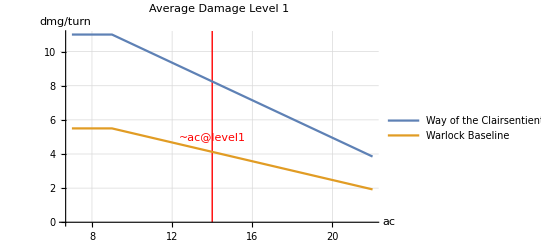

```mathematica
(*For[n=1,n<=20,n++,*)
With[{
level=1(*n if export run*),
acMin=7,acMaxOverwrite={True,22},
showWayOfTheClairsentient01=True,
showWarlockBaseline=True
}
,
With[{acMax=If[acMaxOverwrite[[1]],acMaxOverwrite[[2]],If[level<=8,20,If[level<=16,24,30]]]},
(*Export[StringJoin["comparison",ToString[level],".pdf"],*)
Show[
ListLinePlot[
{
If[showWayOfTheClairsentient01,
With[{asm=If[level<4,3,If[level<6,4,5]],label="Way of the Clairsentient 01",attacks=1+If[level>=5,1,0]},
With[{sharpshooter=True,modifier="normal"},
With[{
toHit=2+asm+proficiencyBonus[level],
dmgNormal=2d[10],
dmgCrit=4d[10]
},
Legended[Table[{ac,attacks((pSuccess[ac-toHit,modifier]-pSuccess[21,modifier])dmgNormal+pSuccess[21,modifier]dmgCrit)},{ac,acMin,acMax}],label]
]
]
],Nothing],
If[showWarlockBaseline,
With[{
asm=If[level<4,3,If[level<8,4,5]],
label="Warlock Baseline",
attacks=Piecewise[{{1,level<5},{2,level<11},{3,level<17},{4,level>=17}}],
modifier="normal"
},
With[{
toHit=2+asm+proficiencyBonus[level],
dmgNormal=d[10]+If[level>=2,asm,0],
dmgCrit=2d[10]+If[level>=2,asm,0]
},
Legended[Table[{ac,attacks((pSuccess[ac-toHit,modifier]-pSuccess[21,modifier])dmgNormal+pSuccess[21,modifier]dmgCrit)},{ac,acMin,acMax}],label]
]
],Nothing]
(*,{Callout[{15,24},"avg. melee damage"]}*)
},
(*Filling->Axis,*)
PlotRange->All,
GridLines->Automatic,
ImageSize->Scaled[0.75],
PlotLabel->StringJoin["Average Damage Level ",ToString[level]],
AxesLabel->{"ac","dmg/turn"},
Prolog->{
Thin, Red, 
Line[{{defaultAC[level],0},{defaultAC[level],1000}}],
Text[StringJoin["~ac@level",ToString[level]],{defaultAC[level],5}]
},
Epilog->{}
],
Graphics[{
(*
Thick,Red,
Circle[{15,24},{1/5,4}]*)
}]
]
]
]
(*] Export*)
(*] For*)
```